```mathematica
Remove["Global`*"]
```

# Monte - Carlo Simulation: Random Walk in 1 Dimension

In a 1 dimensional random walk, the walker starts from the origin and takes one step forward with probability p and backward with probability (1-p) and walks a total of N steps. 
The total displacement from the origin is given by the final position of the walker. To obtain an approximation for the distribution of the final displacement from the origin, we do a Monte Carlo sampling. We write a code to simulate the walk of N steps and run it many times and take an average to get the approximate distribution. More the number of iterates, more accurate the result is compared to the theoretical expressions. 
The 1D random walk follows the binomial distribution.  The probability of taking n1 steps to the right out of a total of N steps is P(n) = (N!)/(n1!(N-n1)!)p^n1(1-p)^(N-n1).
The mean number of steps forward <n1> = pN.
The variance is given by <n1^2> = Np(1-p)
and the root mean square deviation is given by √(Np(1-p)).

## 1. Simulating a random walk

A 1d walk with p given by a pseudorandom number, N=100 steps with 1000 iterations. The plots of the walk, histogram, mean and variance are given below:

0.406234

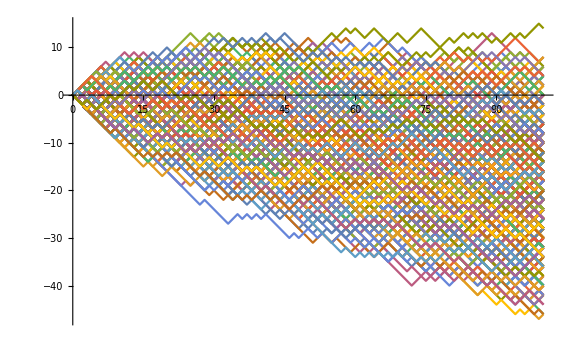

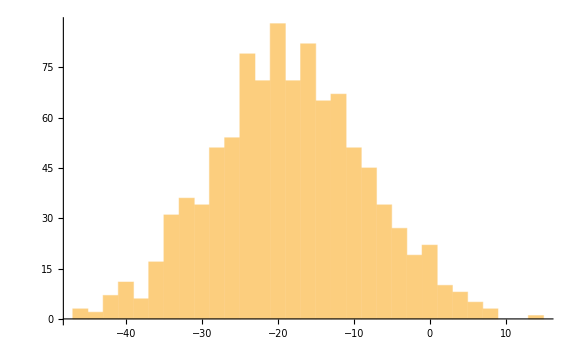

-462/25

505208/4995

```mathematica
p = RandomReal[{0,1}]
data=RandomFunction[RandomWalkProcess[p],{0,100},1000];
ListLinePlot[data]
hist = data[[2,1]][[All,-1]];
Histogram[hist]
Mean[hist]
Variance[hist]
```

a) The value of only one walk - x - is of no interest. We need to do multiple iterations to obtain the distribution function for the displacement from the origin. 
b) The exact distribution cannot be obtained with the monte carlo sampling. Only an approximation can be obtained.

## 2. Variation of histogram with N

### 2.1. For a random p

To observe the variation of the histogram with N, I have varied N as {20, 50, 75, 100, 200} and plotted the corresponding histograms.

0.723616

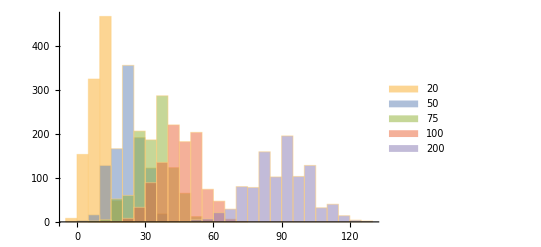

```mathematica
p1 = RandomReal[{0,1}]
data2=RandomFunction[RandomWalkProcess[p1],{0,20},1000];
h2 = data2[[2,1]][[All,-1]];
data3=RandomFunction[RandomWalkProcess[p1],{0,50},1000];
h3 = data3[[2,1]][[All,-1]];
data4=RandomFunction[RandomWalkProcess[p1],{0,75},1000];
h4 = data4[[2,1]][[All,-1]];
data5=RandomFunction[RandomWalkProcess[p1],{0,100},1000];
h5 = data5[[2,1]][[All,-1]];
data6=RandomFunction[RandomWalkProcess[p1],{0,200},1000];
h6 = data6[[2,1]][[All,-1]];
Histogram[{h2,h3,h4,h5,h6}, ChartLegends->{20, 50, 75, 100, 200}]
```

As observed, with the increase in N, the displacement from the origin increases, since p in not equal to 0.5. The width of the histogram signifies the variance. Hence the variance increases with increase in N.

### 2.2. For p = 0.5

0.5

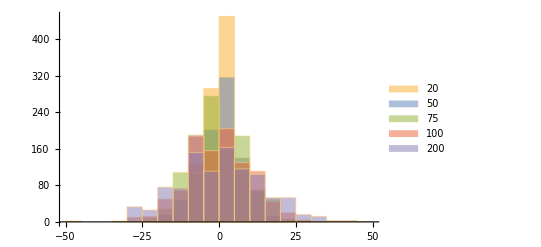

```mathematica
p1 = 0.5
data2=RandomFunction[RandomWalkProcess[p1],{0,20},1000];
h2 = data2[[2,1]][[All,-1]];
data3=RandomFunction[RandomWalkProcess[p1],{0,50},1000];
h3 = data3[[2,1]][[All,-1]];
data4=RandomFunction[RandomWalkProcess[p1],{0,75},1000];
h4 = data4[[2,1]][[All,-1]];
data5=RandomFunction[RandomWalkProcess[p1],{0,100},1000];
h5 = data5[[2,1]][[All,-1]];
data6=RandomFunction[RandomWalkProcess[p1],{0,200},1000];
h6 = data6[[2,1]][[All,-1]];
Histogram[{h2,h3,h4,h5,h6}, ChartLegends->{20, 50, 75, 100, 200}]
```

c) For  p = 0.5, we can clearly observe the increase in width, hence increase in variance of the distribution with N.

## 3. For N = 16 and N = 32

Plotting for N = 16 and N = 32, p =0.5 and measuring the width visually:

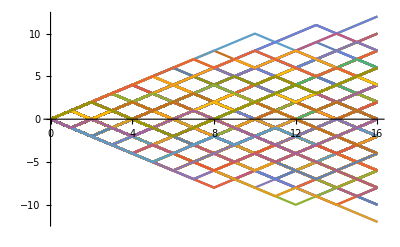

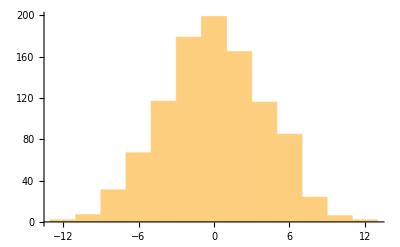

```mathematica
data=RandomFunction[RandomWalkProcess[0.5],{0,16},1000];
ListLinePlot[data]
hist = data[[2,1]][[All,-1]];
Histogram[hist]
Mean[hist]
Variance[hist]
```

Width : 5-(-5) = 10

1/100

159719/9990

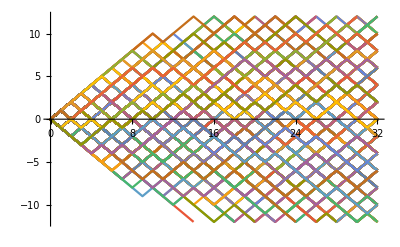

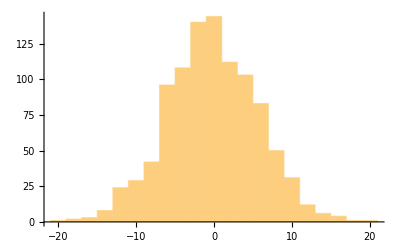

```mathematica
data1=RandomFunction[RandomWalkProcess[0.5],{0,32},1000];
ListLinePlot[data1]
hist1 = data1[[2,1]][[All,-1]];
Histogram[hist1]
Mean[hist1]
Variance[hist1]
```

Width = 6 - (-6) = 12

-61/250

4268558/124875

d) The width has increased from 10 to 12 with increase in N from 16 to 32.

## 4. Variation of variance with N

To approximate the variation of the variance of 1d random walk with the number of steps N, I have simulated walks for different N, calculated the variance and obtained the best fit parameter a for the function N^a which approximates the variance with N.

```mathematica
var={};
Do[AppendTo[var, {i, Variance[RandomFunction[RandomWalkProcess[0.5],{0,i},100][[2,1]][[All,-1]]]}], {i, {100,200,300,400,500,600,700,800, 900,1000}}]
var
```

{{100,8339/99},{200,17008/99},{300,238897/825},{400,3939/11},{500,1201939/2475},{600,570688/825},{700,2124259/2475},{800,1561936/2475},{900,260716/275},{1000,2923804/2475}}

```mathematica
A =FindFit[var, {n^a}, {a}, n]
```

{a→1.00875}

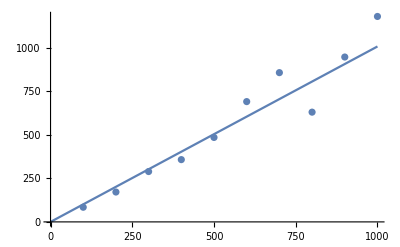

```mathematica
Show[ListPlot[var], Plot[a x/.{A}, {x, 0, 1000}]]
```

As we can see, the best fit is for a ≈ 1 i.e the variance is proportional to N.

## 5. Two dimensional Random Walk

Simulating a 2D random walk:

```mathematica
data = RandomFunction[RandomWalkProcess[0.5],{0,30},2]
```

TemporalData[…]

```mathematica
x = data[[2,1]][[1]]
y = data[[2,1]][[2]]
```

{0,1,0,-1,0,-1,0,1,2,3,2,3,4,3,2,1,2,1,2,1,0,1,0,1,2,1,2,1,2,3,4}

{0,1,0,1,0,1,0,1,2,1,2,1,0,1,2,3,2,1,2,3,4,3,4,3,4,5,4,5,6,5,4}

```mathematica
Transpose[{x,y}]
```

{{0,0},{1,1},{0,0},{-1,1},{0,0},{-1,1},{0,0},{1,1},{2,2},{3,1},{2,2},{3,1},{4,0},{3,1},{2,2},{1,3},{2,2},{1,1},{2,2},{1,3},{0,4},{1,3},{0,4},{1,3},{2,4},{1,5},{2,4},{1,5},{2,6},{3,5},{4,4}}

### Random walk for 1 iteration:

```mathematica
data2d1=RandomFunction[RandomWalkProcess[0.5],{0,100},2];
```

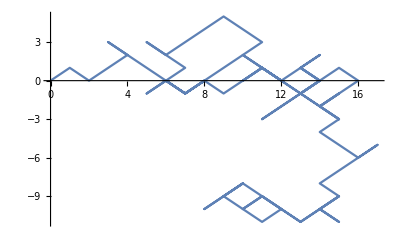

```mathematica
ListLinePlot[Transpose@data2d["States"]]
```

### Histogram of the 2D random walk:

```mathematica
coord2d2 = {};
Do[AppendTo[coord2d2, RandomFunction[RandomWalkProcess[0.75],{0,100},2]["States"][[All,-1]]], {i, 100}]
```

```mathematica
Histogram3D[coord2d2]
```

-Graphics3D-

```mathematica
SmoothHistogram3D[coord2d2]
```

-Graphics3D-

```mathematica
dist1={};
Do[AppendTo[dist1,EuclideanDistance[{0,0}, i]],{i, coord2d2}]
```

```mathematica
N[Mean[dist]]
```

12.4533

```mathematica
N[Variance[dist1]]
```

90.156

### Relation of variance with N:

Undertaking a similar procedure as in 1D walk to find the best fit function for relating variance with N,

```mathematica
var2d = {};
Do[
coord2d = {};
Do[AppendTo[coord2d2, RandomFunction[RandomWalkProcess[0.5],{0,i},2]["States"][[All,-1]]], {i, 100}];
dist={};
Do[AppendTo[dist,EuclideanDistance[{0,0}, j]],{j, coord2d2}];
AppendTo[var2d,{ N[Variance[dist]], i}], {i, {20, 40,60, 80, 100}}]
```

```mathematica
FindFit[var2d, {n^a}, {a}, n]
```

{a→0.728143}

It was observed that the variance varied as N^a, with a around 0.6 - 0.7, the exact conclusive number could not be obtained by this simulation.